```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Hinweis: Befehl Rationalize[…] anwenden, falls Solve::ratnz-Warnung auftritt

## Gerade Gerade (Tangentialellipsen)

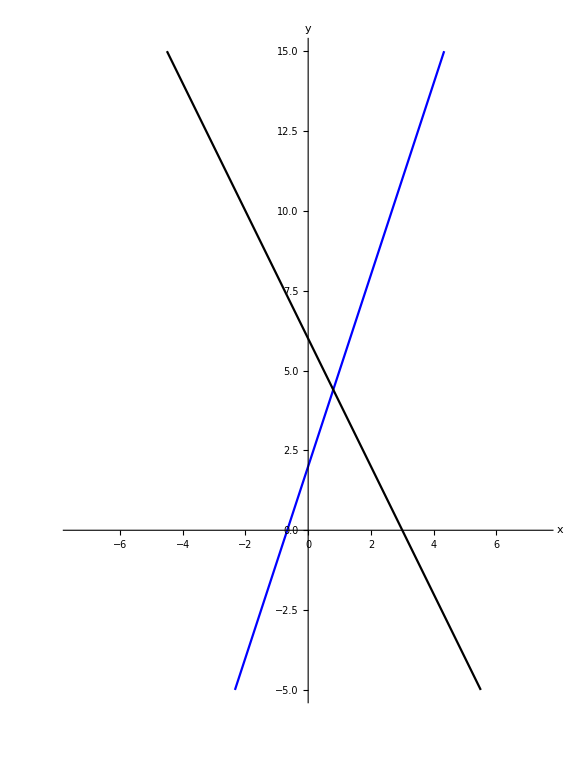

```mathematica
ClearAll["Global`*"]
f[x_]=3x+2;
g[x_]=-2x+6;
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷={2,3};

plot1=Plot[
{f[x],g[x]},
{x,-7.5,7.5},
PlotStyle->{Blue,Black},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-7.5,7.5},{-5,15}},AspectRatio->Automatic,ImageSize->Large];
Print[Show[plot1]]
```

```mathematica
ℯℓℓ𝒾𝓅𝓈ℯ=Solve[1==((x-ellipseMittelpunktX)/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[1]])^2+((y-ellipseMittelpunktY)/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[2]])^2,y];
ellipse1[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[1]];
ellipse2[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[2]];

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{ellipse1[x1]==f[x1]∧ellipse1'[x1]==f'[x1]∨ellipse2[x1]==f[x1]∧ellipse2'[x1]==f'[x1],
ellipse1[x2]==g[x2]∧ellipse1'[x2]==g'[x2]∨ellipse2[x2]==g[x2]∧ellipse2'[x2]==g'[x2]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,ellipseMittelpunktX,ellipseMittelpunktY};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

ellipseMittelpunktY→10.0833 | x1→2.24721 | x2→-1.14164 | ellipseMittelpunktX→0.458359
ellipseMittelpunktY→4.08328 | x1→0.247214 | x2→0.0583592 | ellipseMittelpunktX→-1.54164
ellipseMittelpunktY→4.71672 | x1→1.35279 | x2→1.54164 | ellipseMittelpunktX→3.14164
ellipseMittelpunktY→-1.28328 | x1→-0.647214 | x2→2.74164 | ellipseMittelpunktX→1.14164

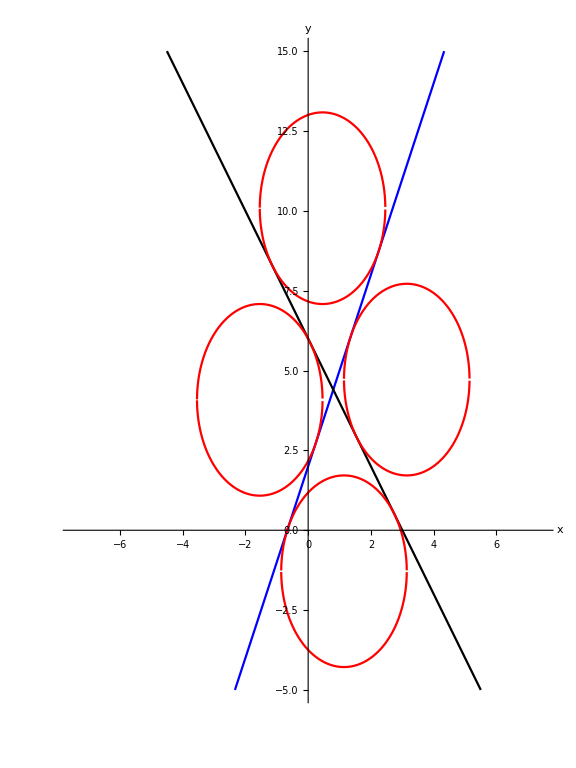

```mathematica
plot2=Plot[
{ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]]},
{x,-7.5,7.5},
PlotStyle->Red];
Print[Show[plot1,plot2]]
```

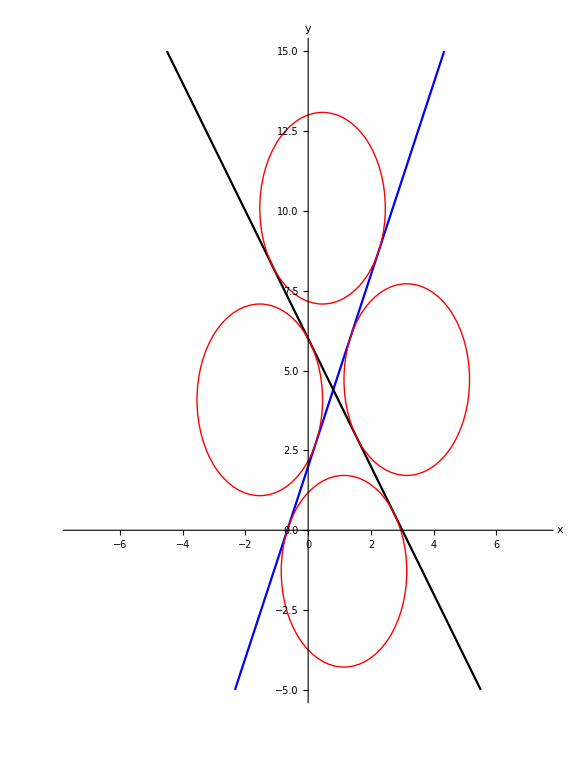

```mathematica
plot2=Graphics[
{{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]}}];
Print[Show[plot1,plot2]]
```

## Gerade Gerade (Tangentialellipsen) (modifiziert)

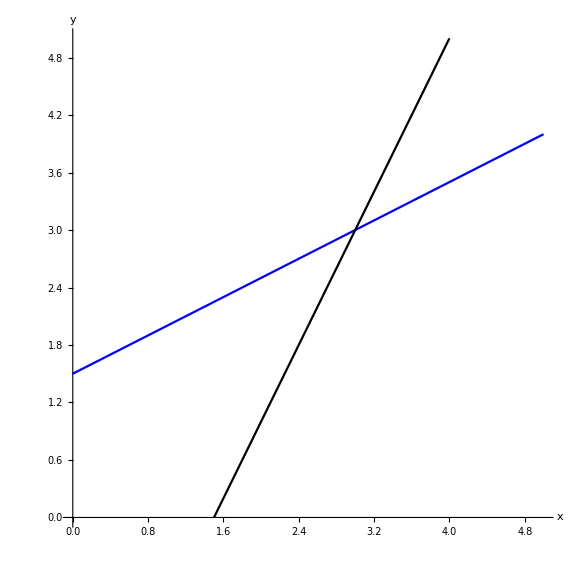

```mathematica
ClearAll["Global`*"]
f[x_]=1/2 x+3/2;
g[x_]=2x-3;
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷={1/2,1/2};

plot1=Plot[
{f[x],g[x]},
{x,0,5},
PlotStyle->{Blue,Black},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{0,5},{0,5}},AspectRatio->Automatic,ImageSize->Large];
Print[Show[plot1]]
```

```mathematica
ℯℓℓ𝒾𝓅𝓈ℯ=Solve[1==((x-ellipseMittelpunktX)/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[1]])^2+((y-ellipseMittelpunktY)/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[2]])^2,y];
ellipse1[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[1]];
ellipse2[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[2]];

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{ellipse1[x1]==f[x1]∧ellipse1'[x1]==f'[x1]∨ellipse2[x1]==f[x1]∧ellipse2'[x1]==f'[x1],
ellipse1[x2]==g[x2]∧ellipse1'[x2]==g'[x2]∨ellipse2[x2]==g[x2]∧ellipse2'[x2]==g'[x2]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,ellipseMittelpunktX,ellipseMittelpunktY};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

ellipseMittelpunktY→3.37268 | x1→2.85093 | x2→3.07454 | ellipseMittelpunktX→2.62732
ellipseMittelpunktY→4.11803 | x1→4.34164 | x2→3.67082 | ellipseMittelpunktX→4.11803
ellipseMittelpunktY→1.88197 | x1→1.65836 | x2→2.32918 | ellipseMittelpunktX→1.88197
ellipseMittelpunktY→2.62732 | x1→3.14907 | x2→2.92546 | ellipseMittelpunktX→3.37268

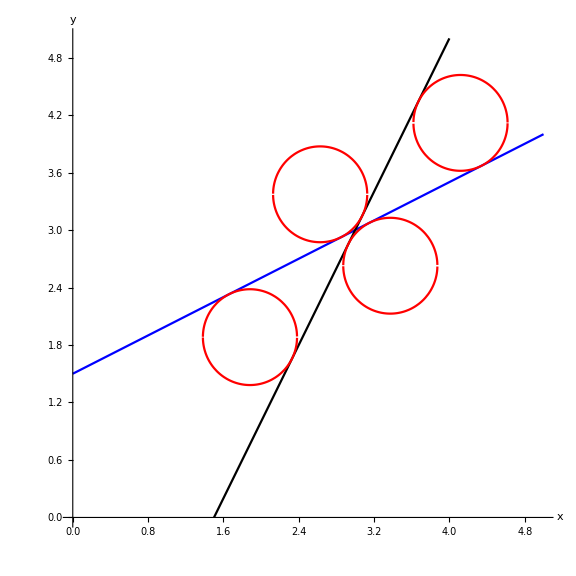

```mathematica
plot2=Plot[
{ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],
ellipse1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],ellipse2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]]},
{x,0,5},
PlotStyle->Red];
Print[Show[plot1,plot2]]
```

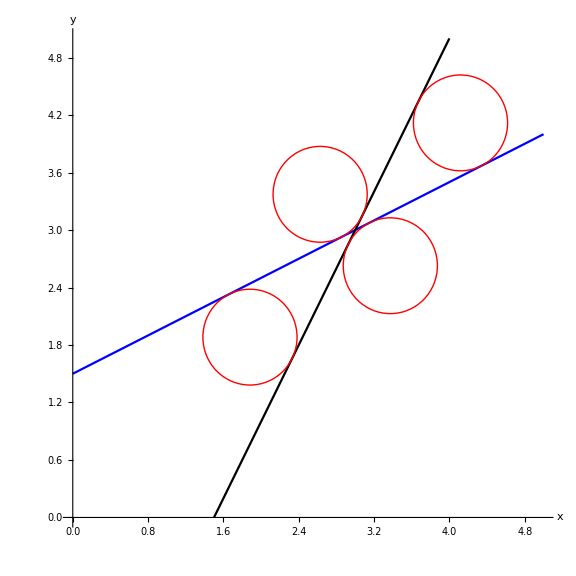

```mathematica
plot2=Graphics[
{{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
{Red,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]}}];
Print[Show[plot1,plot2]]
```

## Gerade Gerade Gerade (Tangentialkreise)

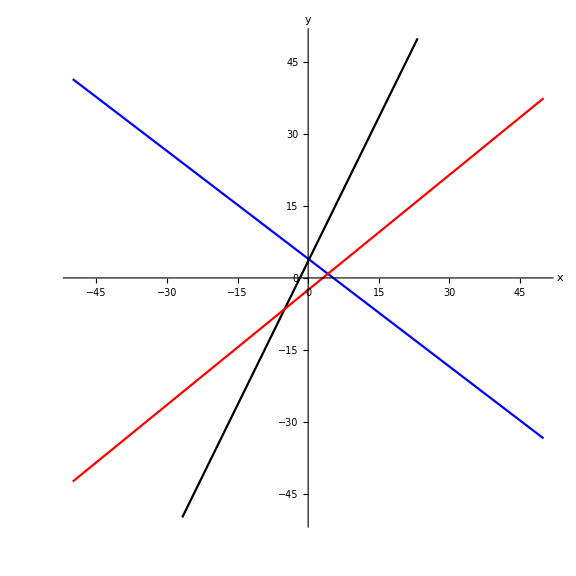

```mathematica
ClearAll["Global`*"]
f[x_]=-3/4 x+4;
g[x_]=2x+7/2;
h[x_]=4/5 x-5/2;

plot1=Plot[
{f[x],g[x],h[x]},
{x,-50,50},
PlotStyle->{Blue,Black,Red},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{-50,50},{-50,50}},AspectRatio->Automatic,ImageSize->Large];
Print[Show[plot1]]
```

```mathematica
𝓀𝓇ℯ𝒾𝓈=Solve[kreisRadius^2==(x-ellipseMittelpunktX)^2+(y-ellipseMittelpunktY)^2,y];
kreis1[x_]=y/.𝓀𝓇ℯ𝒾𝓈[[1]];
kreis2[x_]=y/.𝓀𝓇ℯ𝒾𝓈[[2]];

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{kreis1[x1]==f[x1]∧kreis1'[x1]==f'[x1]∨kreis2[x1]==f[x1]∧kreis2'[x1]==f'[x1],
kreis1[x2]==g[x2]∧kreis1'[x2]==g'[x2]∨kreis2[x2]==g[x2]∧kreis2'[x2]==g'[x2],
kreis1[x3]==h[x3]∧kreis1'[x3]==h'[x3]∨kreis2[x3]==h[x3]∧kreis2'[x3]==h'[x3],
kreisRadius>0};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,x3,ellipseMittelpunktX,ellipseMittelpunktY,kreisRadius};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

ellipseMittelpunktY→4.79614 | x1→2.26232 | x2→1.34485 | x3→6.07859 | kreisRadius→3.1161 | ellipseMittelpunktX→4.13198
ellipseMittelpunktY→0.574522 | x1→-7.15647 | x2→-3.92041 | x3→-6.88505 | kreisRadius→10.991 | ellipseMittelpunktX→-13.7511
ellipseMittelpunktY→0.803456 | x1→2.11305 | x2→-0.897772 | x3→2.1628 | kreisRadius→2.0147 | ellipseMittelpunktX→0.904229
ellipseMittelpunktY→-14.1213 | x1→11.5318 | x2→-6.16304 | x3→-2.96925 | kreisRadius→11.8406 | ellipseMittelpunktX→4.42749

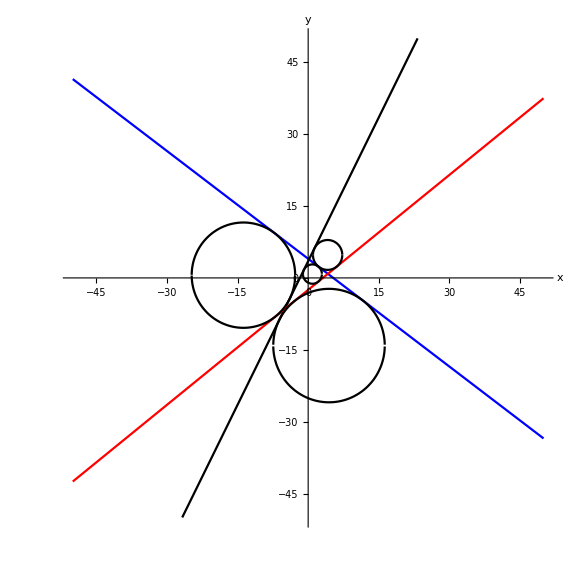

```mathematica
plot2=Plot[
{kreis1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],kreis2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],
kreis1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],kreis2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],
kreis1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],kreis2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],
kreis1[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],kreis2[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]]},
{x,-50,50},
PlotStyle->Black];
Print[Show[plot1,plot2]]
```

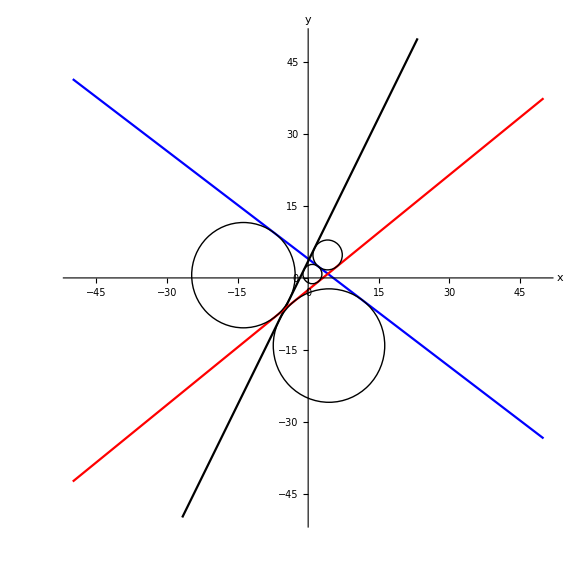

```mathematica
plot2=Graphics[
{{Black,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],kreisRadius/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]]]},
{Black,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],kreisRadius/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]]},
{Black,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],kreisRadius/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]]]},
{Black,Circle[{ellipseMittelpunktX,ellipseMittelpunktY}/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]],kreisRadius/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]]]}}];
Print[Show[plot1,plot2]]
```

## Ellipse (Tangenten)

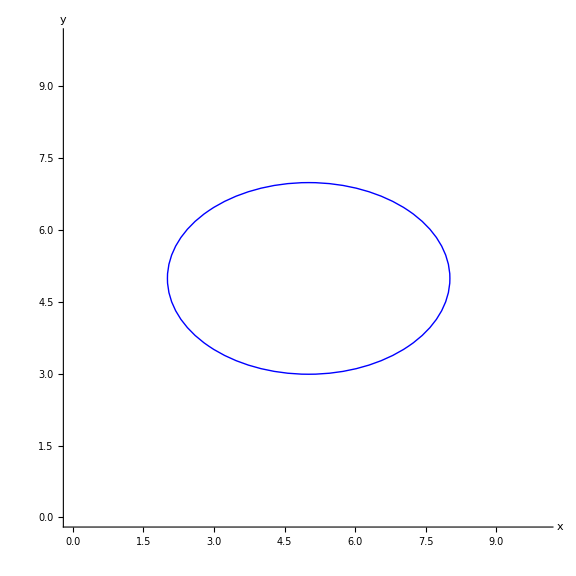

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={5,5};
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷={3,2};
geradeSteigung=1/2;

plot1=Graphics[
{Blue,Circle[ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{0,10},{0,10}},ImageSize->Large];
Print[Show[plot1]]
```

```mathematica
ℯℓℓ𝒾𝓅𝓈ℯ=Solve[1==((x-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[2]])^2,y];
ellipse1[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[1]];
ellipse2[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[2]];
f[x_]=geradeSteigung x+b;

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{ellipse1[x1]==f[x1]∧ellipse1'[x1]==f'[x1]∨ellipse2[x2]==f[x2]∧ellipse2'[x2]==f'[x2]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,b};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(142003 b)/115806+(40299 x1)/38602-(69046 x2)/57903 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(142003 b)/115806-(69046 x1)/57903+(40299 x2)/38602 == 1.

x1→6.8 | x2→5.11466 | b→0.
x1→-3.17868 | x2→3.2 | b→5.

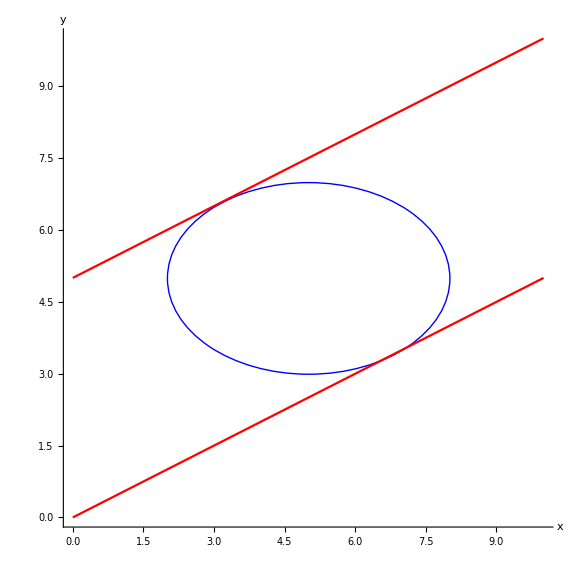

```mathematica
plot2=Plot[
{f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]},
{x,0,10},
PlotStyle->Red];
Print[Show[plot1,plot2]]
```

## Ellipse (Tangenten) (modifiziert)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={5,5};
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷={3,2};
geradeYAchsenabschnitt=2;

plot1=Graphics[
{Blue,Circle[ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷]},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{0,10},{0,10}},ImageSize->Large];
Print[Show[plot1]]
```

-Graphics-

```mathematica
ℯℓℓ𝒾𝓅𝓈ℯ=Solve[1==((x-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷[[2]])^2,y];
ellipse1[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[1]];
ellipse2[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ[[2]];
f[x_]=a x+geradeYAchsenabschnitt;

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{ellipse1[x1]==f[x1]∧ellipse1'[x1]==f'[x1]∨ellipse2[x2]==f[x2]∧ellipse2'[x2]==f'[x2]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,a};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(142003 a)/115806+(40299 x1)/38602-(69046 x2)/57903 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(142003 a)/115806-(69046 x1)/57903+(40299 x2)/38602 == 1.

x1→5.80178 | x2→4.0506 | a→0.1849
x1→-0.64241 | x2→2.20926 | a→1.6901

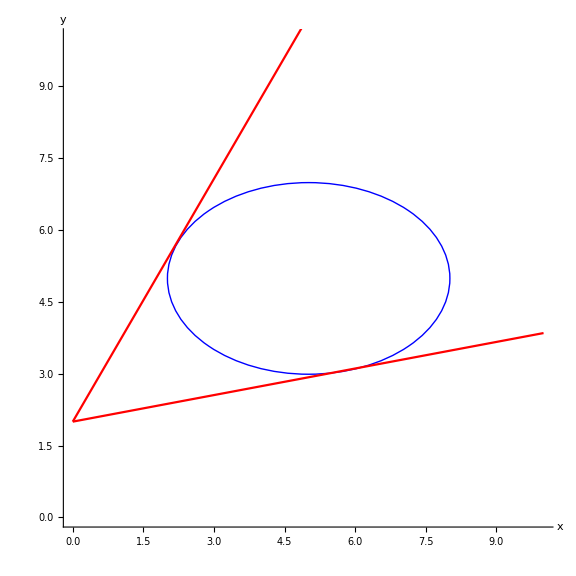

```mathematica
plot2=Plot[
{f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]},
{x,0,10},
PlotStyle->Red];
Print[Show[plot1,plot2]]
```

## Ellipse Ellipse (Tangenten)

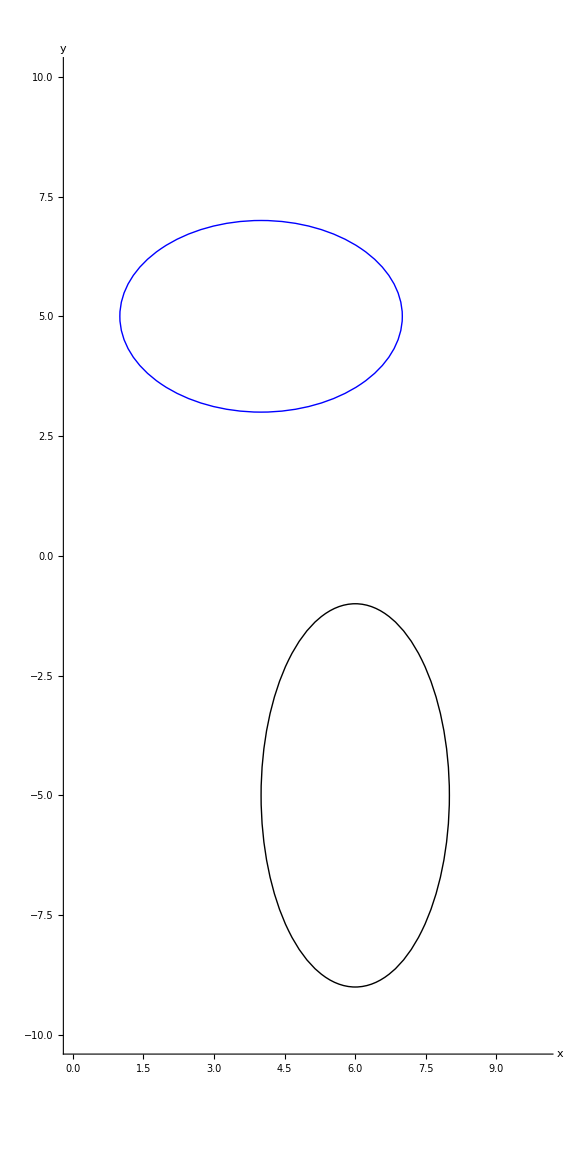

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={4,5};
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷1={3,2};
ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={6,-5};
ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷2={2,4};

plot1=Graphics[
{{Blue,Circle[ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷1]},
{Black,Circle[ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷2]}},
Axes->True,AxesLabel->{"x","y"},PlotRange->{{0,10},{-10,10}},ImageSize->Large];
Print[Show[plot1]]
```

```mathematica
ℯℓℓ𝒾𝓅𝓈ℯ1=Solve[1==((x-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷1[[2]])^2,y];
ellipse11[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ1[[1]];
ellipse12[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ1[[2]];
ℯℓℓ𝒾𝓅𝓈ℯ2=Solve[1==((x-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℯ𝒜𝒷2[[2]])^2,y];
ellipse21[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ2[[1]];
ellipse22[x_]=y/.ℯℓℓ𝒾𝓅𝓈ℯ2[[2]];
f[x_]=a x+b;

ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{ellipse11[x1]==f[x1]∧ellipse11'[x1]==f'[x1]∧ellipse21[x2]==f[x2]∧ellipse21'[x2]==f'[x2]∨
ellipse11[x3]==f[x3]∧ellipse11'[x3]==f'[x3]∧ellipse22[x4]==f[x4]∧ellipse22'[x4]==f'[x4]∨

ellipse12[x5]==f[x5]∧ellipse12'[x5]==f'[x5]∧ellipse21[x6]==f[x6]∧ellipse21'[x6]==f'[x6]∨
ellipse12[x7]==f[x7]∧ellipse12'[x7]==f'[x7]∧ellipse22[x8]==f[x8]∧ellipse22'[x8]==f'[x8]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x1,x2,x3,x4,x5,x6,x7,x8,a,b};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with (48047 a)/58453-(122114 b)/175359-(109178 x1)/175359+(113248 x2)/175359-(42051 x3)/58453-(102452 x4)/175359+(153391 x5)/175359-(52395 x6)/58453+(108332 x7)/175359-(43121 x8)/58453 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with -(183319 a)/144328-(141637 b)/144328+(33931 x1)/36082-(24131 x2)/18041+(92131 x3)/72164+(58705 x4)/72164-(12627 x5)/18041+(67945 x6)/72164+(111493 x7)/144328+(88207 x8)/72164 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 3. Returning intersection of solutions with (57051 a)/56189+(14252 b)/8027+(96038 x1)/56189+(185515 x2)/112378-(137107 x3)/112378+(9659 x4)/8027+(12403 x5)/8027-(172407 x6)/112378-(117953 x7)/112378-(162067 x8)/112378 == 1.

General::stop: Further output of NSolve::infsolns will be suppressed during this calculation.

x1→1.04971 | x2→4.2498 | x3→90.5615 | x4→-27.2987 | x5→78.0763 | x6→74.7999 | x7→-4.18073 | x8→-79.0161 | a→-3.61652 | b→8.43372
x1→105.597 | x2→-30.5157 | x3→1.51511 | x4→6.88405 | x5→93.5191 | x6→92.6147 | x7→-9.57535 | x8→-91.2488 | a→-0.985559 | b→5.37265
x1→-90.9514 | x2→20.1241 | x3→6.92022 | x4→4.36619 | x5→-70.8292 | x6→-62.8871 | x7→0.971983 | x8→79.9975 | a→2.83268 | b→-15.0609
x1→695.58 | x2→-209.547 | x3→572.547 | x4→543.943 | x5→-35.1728 | x6→-603.518 | x7→6.99288 | x8→7.95846 | a→-9.65917 | b→72.6831

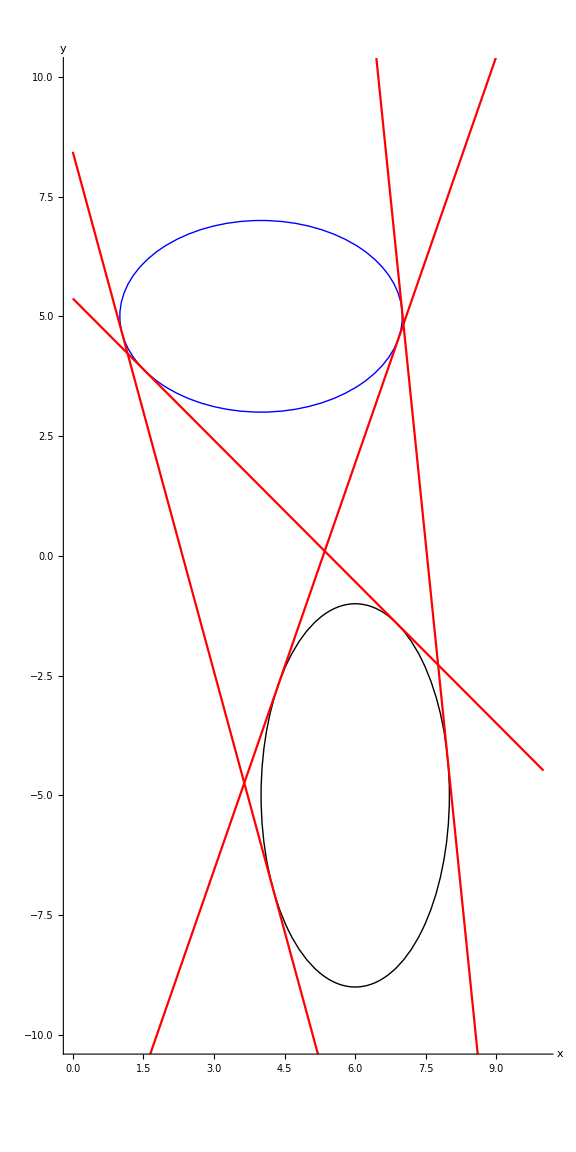

```mathematica
plot2=Plot[
{f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]],f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]],f[x]/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]]},
{x,0,10},
PlotStyle->{Red}];
Print[Show[plot1,plot2]]
```

## Spirale Gerade (Schnittpunkte)

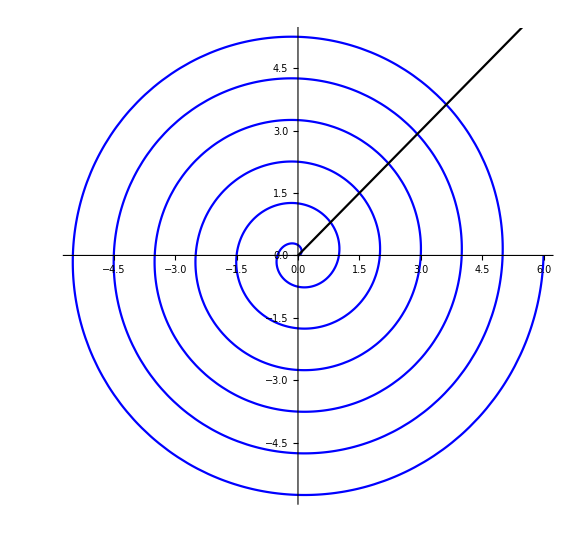

```mathematica
ClearAll["Global`*"]
spiraleAbstand=1;
spiraleWindungen=6;
𝓈𝓅𝒾𝓇𝒶ℓℯ={spiraleAbstand/(2π)γ Cos[γ],spiraleAbstand/(2π) γ Sin[γ]};

plot1=ParametricPlot[
𝓈𝓅𝒾𝓇𝒶ℓℯ,
{γ,0,spiraleWindungen 2 π},
PlotStyle->Blue,ImageSize->Large];
plot2=Plot[
x,
{x,0,6},
PlotStyle->Black];
Print[Show[plot1,plot2]]
```

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{y==x,
({{x}, {y}})==𝓈𝓅𝒾𝓇𝒶ℓℯ};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0 | y→0 | γ→0
x→ConditionalExpression[0.159155 (0.785398+6.28319 C[1]) Cos[1. (0.785398+6.28319 C[1])], C[1]∈ℤ] | y→ConditionalExpression[0.159155 (0.785398+6.28319 C[1]) Cos[1. (0.785398+6.28319 C[1])], C[1]∈ℤ] | γ→ConditionalExpression[1. (0.785398+6.28319 C[1]), C[1]∈ℤ]
x→ConditionalExpression[0.159155 (-2.35619+6.28319 C[1]) Cos[1. (-2.35619+6.28319 C[1])], C[1]∈ℤ] | y→ConditionalExpression[0.159155 (-2.35619+6.28319 C[1]) Cos[1. (-2.35619+6.28319 C[1])], C[1]∈ℤ] | γ→ConditionalExpression[1. (-2.35619+6.28319 C[1]), C[1]∈ℤ]

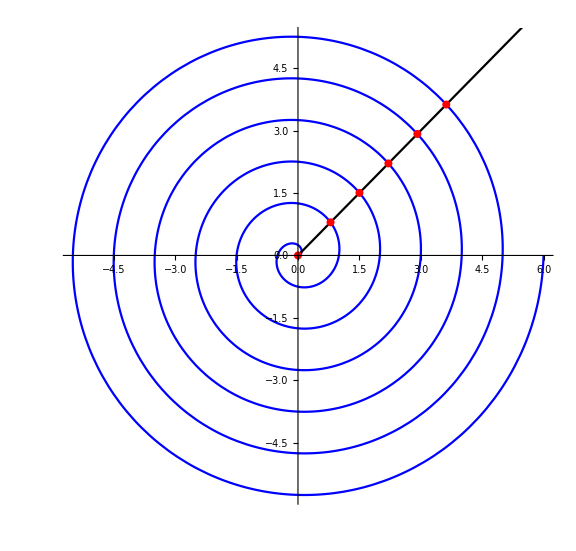

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]/.C[1]->1;
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉3={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]/.C[1]->2;
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉4={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]/.C[1]->3;
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉5={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]/.C[1]->4;
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉6={x,y}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]]/.C[1]->5;

plot3=Graphics[
{{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1]},
{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2]},
{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉3]},
{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉4]},
{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉5]},
{Red,PointSize[.01],Point[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉6]}}];
Print[Show[plot1,plot2,plot3]]
```

## Ellipsoid Gerade (Schnittpunkte)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={1,2,3};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={3/2,3,3/2};
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1={0,0,0};
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2={2,3,4};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
{Black,Thick,InfiniteLine[{ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1,ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2}]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,5},{-1,5},{-1,5}},ImageSize->Large];
Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1+γ(ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2-ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1),
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→2. | y→3. | z→4. | γ→1.
x→0.786517 | y→1.17978 | z→1.57303 | γ→0.393258

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot2=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.1]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.1]}}];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ebene (Schnittkurve)

z=1/3(1-x-2y)
→𝓅_1=(1,0,0), 𝓅_2=(0,1/2,0), 𝓅_3=(0,0,1/3)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1,1,1};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1={1,0,0};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2={0,1/2,0};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3={0,0,1/3};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
{Black,Opacity[.5],InfinitePlane[{𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3}]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1+γ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1)+δ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1),
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,γ,δ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[1.-3. z+0.8 (-1.+3. z)-0.565685 √(2.+3. z-7. z^2), -0.36159<z<0.790161] | y→ConditionalExpression[0.5 (-0.8 (-1.+3. z)+0.565685 √(2.+3. z-7. z^2)), -0.36159<z<0.790161] | γ→ConditionalExpression[-0.8 (-1.+3. z)+0.565685 √(2.+3. z-7. z^2), -0.36159<z<0.790161] | δ→ConditionalExpression[3. z, -0.36159<z<0.790161]
x→ConditionalExpression[1.-3. z+0.8 (-1.+3. z)+0.565685 √(2.+3. z-7. z^2), -0.36159<z<0.790161] | y→ConditionalExpression[0.5 (-0.8 (-1.+3. z)-0.565685 √(2.+3. z-7. z^2)), -0.36159<z<0.790161] | γ→ConditionalExpression[-0.8 (-1.+3. z)-0.565685 √(2.+3. z-7. z^2), -0.36159<z<0.790161] | δ→ConditionalExpression[3. z, -0.36159<z<0.790161]

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{z==1/3(1-x-2y),
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,γ,δ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

x→ConditionalExpression[1.-3. z-2. (-0.4 (-1.+3. z)-0.282843 √(2.+3. z-7. z^2)), -0.36159<z<0.790161] | y→ConditionalExpression[-0.4 (-1.+3. z)-0.282843 √(2.+3. z-7. z^2), -0.36159<z<0.790161]
x→ConditionalExpression[1.-3. z-2. (-0.4 (-1.+3. z)+0.282843 √(2.+3. z-7. z^2)), -0.36159<z<0.790161] | y→ConditionalExpression[-0.4 (-1.+3. z)+0.282843 √(2.+3. z-7. z^2), -0.36159<z<0.790161]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z}},
{z,-.362,.791},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ellipsoid (Schnittkurve)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={1,2,3};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1={3/2,3,3/2};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={1,3,4};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2={3/2,3,3/2};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1]},
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,6},{-1,6},{-1,6}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[1.-0.25 √(-949.+560. z-80. z^2), 3.375<z<4.12249] | y→ConditionalExpression[3.-1. √(-59.+32. z-4. z^2+8. (1.-0.25 √(-949.+560. z-80. z^2))-4. (1.-0.25 √(-949.+560. z-80. z^2))^2), 3.375<z<4.12249]
x→ConditionalExpression[1.-0.25 √(-949.+560. z-80. z^2), 2.87751<z<3.375] | y→ConditionalExpression[3.+√(-59.+32. z-4. z^2+8. (1.-0.25 √(-949.+560. z-80. z^2))-4. (1.-0.25 √(-949.+560. z-80. z^2))^2), 2.87751<z<3.375]
x→ConditionalExpression[1.+0.25 √(-949.+560. z-80. z^2), 3.375<z<4.12249] | y→ConditionalExpression[3.-1. √(-59.+32. z-4. z^2+8. (1.+0.25 √(-949.+560. z-80. z^2))-4. (1.+0.25 √(-949.+560. z-80. z^2))^2), 3.375<z<4.12249]
x→ConditionalExpression[1.+0.25 √(-949.+560. z-80. z^2), 2.87751<z<3.375] | y→ConditionalExpression[3.+√(-59.+32. z-4. z^2+8. (1.+0.25 √(-949.+560. z-80. z^2))-4. (1.+0.25 √(-949.+560. z-80. z^2))^2), 2.87751<z<3.375]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,2]],z}},
{z,2.877,4.123},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ellipsoid (Schnittebene)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={1,2,3};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1={3/2,3,3/2};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={1,3,4};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2={3/2,3,3/2};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1]},
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,6},{-1,6},{-1,6}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2==
((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={z};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

z→4.125-0.25 y

```mathematica
plot2=Plot3D[
z/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],
{x,-1,6},{y,-1,6},
PlotStyle->Directive[Red,Opacity[.5]]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ellipsoid (Schnittebene) (modifiziert)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={1,1,1};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1={5,5,5};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={5,5,5};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2={3,3,3};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1]},
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-5,10},{-5,10},{-5,10}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2==
((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={z};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

z→ConditionalExpression[7.25-0.25 √(-1007.+232. x-16. x^2+232. y-16. y^2), ]
z→ConditionalExpression[7.25+0.25 √(-1007.+232. x-16. x^2+232. y-16. y^2), ]

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{(x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])^2+(y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])^2+(z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])^2-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]]^2==
(x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])^2+(y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])^2+(z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])^2-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]]^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={z};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

z→11.-1. x-1. y

```mathematica
plot2=Plot3D[
z/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]],
{x,-1,6},{y,-1,6},
PlotStyle->Directive[Red,Opacity[.5]]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ellipsoid Ellipsoid (Schnittpunkte)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={1,2,3};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1={3/2,3,3/2};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={1,3,4};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2={3/2,3,3/2};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉3={1,0,4};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸3={1,1,1};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1]},
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2]},
{Red,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉3,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸3]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,6},{-1,6},{-1,6}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉3[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸3[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉3[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸3[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉3[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸3[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0.150489 | y→0.527525 | z→3.99312
x→1.84951 | y→0.527525 | z→3.99312

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot2=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.1]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.1]}}];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Ellipsoid Ebene (Schnittpunkte)

z=x+2y
→𝓅_1=(0,0,0), 𝓅_2=(1,0,1), 𝓅_3=(0,1/2,1)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={-1,-1,-1};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1={2,2,2};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={1,1,1};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2={3,3,3};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1={0,0,0};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2={1,0,1};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3={0,1/2,1};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1]},
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2]},
{Black,Opacity[.5],InfinitePlane[{𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3}]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->Large];
Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1+γ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1)+δ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1),
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ,δ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→-1.70604 | y→0.720691 | z→-0.264654 | γ→-1.70604 | δ→1.44138
x→0.991751 | y→-1.07783 | z→-1.16392 | γ→0.991751 | δ→-2.15567

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{z==x+2y,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸1[[3]])^2,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸2[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0.991751 | y→-1.07783 | z→-1.16392
x→-1.70604 | y→0.720691 | z→-0.264654

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot2=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.25]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.25]}}];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Kegel (Schnittkurve)

```mathematica
ClearAll["Global`*"]
𝒳[α_]=({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}});
𝒴[β_]=({{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}});
𝒵[γ_]=({{Cos[γ], -Sin[γ], 0}, {Sin[γ], Cos[γ], 0}, {0, 0, 1}});

ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1,1,1};
kegelRadius=1;
kegelHoehe=2;
𝓀ℯℊℯℓℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉=({{0}, {1}, {-1}});
𝓀ℯℊℯℓ[γ_,h_]=FullSimplify[N[𝒵[γ].(({{kegelRadius}, {0}, {0}})+({{-(kegelRadius h)/kegelHoehe}, {0}, {h}}))+𝓀ℯℊℯℓℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉]];

plot1=Graphics3D[
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];
plot2=ParametricPlot3D[
𝓀ℯℊℯℓ[γ,h],
{γ,0,2π},{h,0,kegelHoehe},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2,
({{x}, {y}, {z}})==𝓀ℯℊℯℓ[γ,h]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,h};
ℓℴℯ𝓈𝓊𝓃ℊ=FullSimplify[TrigReduce[NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals]]];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x→ConditionalExpression[Cos[γ] (0.4+1. √(-0.04 Cos[γ]^2-0.16 Sin[γ])-0.2 Sin[γ]), -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | y→ConditionalExpression[0.9+0.1 Cos[2 γ]+(0.4+1. √(-0.04 Cos[γ]^2-0.16 Sin[γ])) Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | z→ConditionalExpression[0.2-2. √(-0.04 Cos[γ]^2-0.16 Sin[γ])+0.4 Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | h→ConditionalExpression[1.2-2. √(-0.04 Cos[γ]^2-0.16 Sin[γ])+0.4 Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])]
x→ConditionalExpression[Cos[γ] (0.4-1. √(-0.04 Cos[γ]^2-0.16 Sin[γ])-0.2 Sin[γ]), -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | y→ConditionalExpression[0.9+0.1 Cos[2 γ]+(0.4-1. √(-0.04 Cos[γ]^2-0.16 Sin[γ])) Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | z→ConditionalExpression[0.2+2. √(-0.04 Cos[γ]^2-0.16 Sin[γ])+0.4 Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])] | h→ConditionalExpression[1.2+2. √(-0.04 Cos[γ]^2-0.16 Sin[γ])+0.4 Sin[γ], -2. √(-Sin[γ])<Cos[γ]<2. √(-Sin[γ])]

```mathematica
plot3=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,3]]},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,3]]}},
{γ,0,2π},
PlotStyle->Directive[Red,Thick],PlotPoints->100];
Print[Show[plot1,plot2,plot3]]
```

Less::nord: Invalid comparison with 0.-0.0159411 ⅈ attempted.

Less::nord: Invalid comparison with 0.+0.0159411 ⅈ attempted.

Less::nord: Invalid comparison with 0.-0.0159411 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

-Graphics3D-

## Ellipsoid Kegel (Schnittkurve) (modifiziert)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1,1,1};
kegelHoehe=2;
𝓀ℯℊℯℓ[γ_,h_]=({{h/2 Cos[γ]}, {1+h/2 Sin[γ]}, {1+h}});

plot1=Graphics3D[
{Black,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];
plot2=ParametricPlot3D[
𝓀ℯℊℯℓ[γ,h],
{γ,0,2π},{h,0,-kegelHoehe},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2,
({{x}, {y}, {z}})==𝓀ℯℊℯℓ[γ,h]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,h};
ℓℴℯ𝓈𝓊𝓃ℊ=FullSimplify[TrigReduce[NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals]]];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[Cos[γ] (-0.4-1. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.2 Sin[γ]), -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | y→ConditionalExpression[0.9+0.1 Cos[2 γ]+(-0.4-1. √(-0.04 Cos[γ]^2+0.16 Sin[γ])) Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | z→ConditionalExpression[0.2-2. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.4 Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | h→ConditionalExpression[-0.8-2. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.4 Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]]
x→ConditionalExpression[Cos[γ] (-0.4+1. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.2 Sin[γ]), -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | y→ConditionalExpression[0.9+0.1 Cos[2 γ]+(-0.4+1. √(-0.04 Cos[γ]^2+0.16 Sin[γ])) Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | z→ConditionalExpression[0.2+2. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.4 Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]] | h→ConditionalExpression[-0.8+2. √(-0.04 Cos[γ]^2+0.16 Sin[γ])-0.4 Sin[γ], -2. √Sin[γ]<Cos[γ]<2. √Sin[γ]]

```mathematica
plot3=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,3]]},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,3]]}},
{γ,0,2π},
PlotStyle->Directive[Red,Thick],PlotPoints->100];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Kegel Gerade (Schnittpunkte)

```mathematica
ClearAll["Global`*"]
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1={0,0,2};
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2={2,3,4};
kegelRadius=5;
kegelHoehe=10;
𝓀ℯℊℯℓ=Solve[(kegelRadius-z kegelRadius/kegelHoehe)^2==x^2+y^2,z,Reals];
kegel=z/.𝓀ℯℊℯℓ[[1]];

plot1=Graphics3D[
{Black,Thick,InfiniteLine[{ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1,ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2}]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-10,10},{-10,10},{-10,10}},ImageSize->Large];
plot2=Plot3D[
kegel,
{x,-10,10},{y,-10,10},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1+γ(ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2-ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1),
(kegelRadius-z kegelRadius/kegelHoehe)^2==x^2+y^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→1.73703 | y→2.60555 | z→3.73703 | γ→0.868517
x→-3.07037 | y→-4.60555 | z→-1.07037 | γ→-1.53518

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot3=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.5]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.5]}}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Kegel Ebene (Schnittkurve)

z=1/8(10-x-2y)
→𝓅_1=(0,0,5/4), 𝓅_2=(0,5,0), 𝓅_3=(10,0,0)

```mathematica
ClearAll["Global`*"]
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1={0,0,5/4};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2={0,5,0};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3={10,0,0};
kegelRadius=5;
kegelHoehe=10;
𝓀ℯℊℯℓ=Solve[(kegelRadius-z kegelRadius/kegelHoehe)^2==x^2+y^2,z,Reals];
kegel=z/.𝓀ℯℊℯℓ[[1]];

plot1=Graphics3D[
{Black,Opacity[.5],InfinitePlane[{𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3}]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-10,10},{-10,10},{-10,10}},ImageSize->Large];
plot2=Plot3D[
kegel,
{x,-10,10},{y,-10,10},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1+γ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1)+δ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1),
(kegelRadius-z kegelRadius/kegelHoehe)^2==x^2+y^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,γ,δ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[10. (0.04 (5.-4. z)-0.02 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | y→ConditionalExpression[5.-4. z-5. (0.04 (5.-4. z)-0.02 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | γ→ConditionalExpression[0.2 (5.-4. z-5. (0.04 (5.-4. z)-0.02 √(100.+540. z-251. z^2))), -0.171512<z<2.32291] | δ→ConditionalExpression[0.04 (5.-4. z)-0.02 √(100.+540. z-251. z^2), -0.171512<z<2.32291]
x→ConditionalExpression[10. (0.04 (5.-4. z)+0.02 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | y→ConditionalExpression[5.-4. z-5. (0.04 (5.-4. z)+0.02 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | γ→ConditionalExpression[0.2 (5.-4. z-5. (0.04 (5.-4. z)+0.02 √(100.+540. z-251. z^2))), -0.171512<z<2.32291] | δ→ConditionalExpression[0.04 (5.-4. z)+0.02 √(100.+540. z-251. z^2), -0.171512<z<2.32291]

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{z==1/8(10-x-2y),
(kegelRadius-z kegelRadius/kegelHoehe)^2==x^2+y^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[10.-8. z-2. (-0.8 (-5.+4. z)-0.1 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | y→ConditionalExpression[-0.8 (-5.+4. z)-0.1 √(100.+540. z-251. z^2), -0.171512<z<2.32291]
x→ConditionalExpression[10.-8. z-2. (-0.8 (-5.+4. z)+0.1 √(100.+540. z-251. z^2)), -0.171512<z<2.32291] | y→ConditionalExpression[-0.8 (-5.+4. z)+0.1 √(100.+540. z-251. z^2), -0.171512<z<2.32291]

```mathematica
plot3=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z}},
{z,-.172,2.323},
PlotStyle->{Directive[Red,Thick]}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Torus Gerade (Schnittpunkte)

```mathematica
ClearAll["Global`*"]
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1={0,1,0};
ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2={2,1,2};
𝓉ℴ𝓇𝓊𝓈=Solve[0==(x^2+y^2+z^2)^2-4(x^2+y^2),z,Reals];
torus1=z/.𝓉ℴ𝓇𝓊𝓈[[1]];
torus2=z/.𝓉ℴ𝓇𝓊𝓈[[2]];

plot1=Graphics3D[
{Black,Thick,InfiniteLine[{ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1,ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2}]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];
plot2=Plot3D[
{torus1,torus2},
{x,-2,2},{y,-2,2},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1+γ(ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉2-ℊℯ𝓇𝒶𝒹ℯ𝒫𝓊𝓃𝓀𝓉1),
0==(x^2+y^2+z^2)^2-4(x^2+y^2)};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

y→1. | x→-0.930605 | z→-0.930605 | γ→-0.465302
y→1. | x→0.930605 | z→0.930605 | γ→0.465302

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot3=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.1]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.1]}}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Torus Ebene (Schnittkurve)

z=1/8(10-x-2y)
→𝓅_1=(0,0,5/4), 𝓅_2=(0,5,0), 𝓅_3=(10,0,0)

```mathematica
ClearAll["Global`*"]
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1={0,0,5/4};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2={0,5,0};
𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3={10,0,0};
𝓉ℴ𝓇𝓊𝓈=Solve[0==(x^2+y^2+z^2)^2-4(x^2+y^2),z,Reals];
torus1=z/.𝓉ℴ𝓇𝓊𝓈[[1]];
torus2=z/.𝓉ℴ𝓇𝓊𝓈[[2]];

plot1=Graphics3D[
{Black,Opacity[.5],InfinitePlane[{𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2,𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3}]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];
plot2=Plot3D[
{torus1,torus2},
{x,-2,2},{y,-2,2},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1+γ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉2-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1)+δ(𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉3-𝒻ℓ𝒶ℯ𝒸𝒽ℯ𝒫𝓊𝓃𝓀𝓉1),
0==(x^2+y^2+z^2)^2-4(x^2+y^2)};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,γ,δ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[10. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,1], 0.804462<z<0.99587||0.99587<z<1.] | y→ConditionalExpression[5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,1], 0.804462<z<0.99587||0.99587<z<1.] | γ→ConditionalExpression[0.2 (5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,1]), 0.804462<z<0.99587||0.99587<z<1.] | δ→ConditionalExpression[Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,1], 0.804462<z<0.99587||0.99587<z<1.]
x→ConditionalExpression[10. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,2], 0.804462<z<0.99587||0.99587<z<1.] | y→ConditionalExpression[5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,2], 0.804462<z<0.99587||0.99587<z<1.] | γ→ConditionalExpression[0.2 (5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,2]), 0.804462<z<0.99587||0.99587<z<1.] | δ→ConditionalExpression[Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,2], 0.804462<z<0.99587||0.99587<z<1.]
x→ConditionalExpression[10. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,3], 0.99587<z<1.] | y→ConditionalExpression[5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,3], 0.99587<z<1.] | γ→ConditionalExpression[0.2 (5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,3]), 0.99587<z<1.] | δ→ConditionalExpression[Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,3], 0.99587<z<1.]
x→ConditionalExpression[10. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,4], 0.99587<z<1.] | y→ConditionalExpression[5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,4], 0.99587<z<1.] | γ→ConditionalExpression[0.2 (5.-4. z-5. Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,4]), 0.99587<z<1.] | δ→ConditionalExpression[Root[525.-1840. z+2386. z^2-1360. z^3+289. z^4+(-2300.+5840. z-4900. z^2+1360. z^3) #1+(8250.-14000. z+5850. z^2) #1^2+(-12500.+10000. z) #1^3+15625. #1^4&,4], 0.99587<z<1.]

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{z==1/8(10-x-2y),
0==(x^2+y^2+z^2)^2-4(x^2+y^2)};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[10.-8. z-2. Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,1], 0.804462<z<0.99587||0.99587<z<1.] | y→ConditionalExpression[Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,1], 0.804462<z<0.99587||0.99587<z<1.]
x→ConditionalExpression[10.-8. z-2. Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,2], 0.804462<z<0.99587||0.99587<z<1.] | y→ConditionalExpression[Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,2], 0.804462<z<0.99587||0.99587<z<1.]
x→ConditionalExpression[10.-8. z-2. Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,3], 0.99587<z<1.] | y→ConditionalExpression[Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,3], 0.99587<z<1.]
x→ConditionalExpression[10.-8. z-2. Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,4], 0.99587<z<1.] | y→ConditionalExpression[Root[9600.-31360. z+38344. z^2-20800. z^3+4225. z^4+(-7840.+19072. z-15440. z^2+4160. z^3) #1+(2580.-4160. z+1674. z^2) #1^2+(-400.+320. z) #1^3+25. #1^4&,4], 0.99587<z<1.]

```mathematica
plot3=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,2]],z}},
{z,.8,1},
PlotStyle->{Directive[Red,Thick]}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Torus Torus (Schnittkurve)

```mathematica
ClearAll["Global`*"]
𝓉ℴ𝓇𝓊𝓈[Δx_]=Solve[0==((x-Δx)^2+y^2+z^2)^2-4((x-Δx)^2+y^2),z,Reals];
torus1[Δx_]=z/.𝓉ℴ𝓇𝓊𝓈[Δx][[1]];
torus2[Δx_]=z/.𝓉ℴ𝓇𝓊𝓈[Δx][[2]];

plot1=Plot3D[
{torus1[0],torus2[0],torus1[1],torus2[1]},
{x,-2,4},{y,-2,2},
PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None,BoxRatios->Automatic,ImageSize->Large];
Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{0==(x^2+y^2+z^2)^2-4(x^2+y^2),
0==((x-1)^2+y^2+z^2)^2-4((x-1)^2+y^2)};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃];(*funktioniert nicht mit ,Reals*)

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0.5 | y→-0.5 √(7.-4. z^2-8. √(1.-1. z^2))
x→0.5 | y→0.5 √(7.-4. z^2-8. √(1.-1. z^2))
x→0.5 | y→-0.5 √(7.-4. z^2+8. √(1.-1. z^2))
x→0.5 | y→0.5 √(7.-4. z^2+8. √(1.-1. z^2))
x→0.5 (1.-4. √(1.-1. z^2)) | y→-0.866025 √(-3.+4. z^2)
x→0.5 (1.-4. √(1.-1. z^2)) | y→0.866025 √(-3.+4. z^2)
x→0.5 (1.+4. √(1.-1. z^2)) | y→-0.866025 √(-3.+4. z^2)
x→0.5 (1.+4. √(1.-1. z^2)) | y→0.866025 √(-3.+4. z^2)

```mathematica
plot2=ParametricPlot3D[
Table[{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[i]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[i]],z},{i,Length[ℓℴℯ𝓈𝓊𝓃ℊ]}],
{z,-2,2},
PlotPoints->500,(*Auflösung erhöhen*)
PlotStyle->{Directive[Red,Thick]}];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Spirale (Schnittpunkte)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1/2,1/2,1/2};
spiraleHoehe=2;
spiraleRadius=3/10;
spiraleWindungen=10;
𝓈𝓅𝒾𝓇𝒶ℓℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,-1};
𝓈𝓅𝒾𝓇𝒶ℓℯ={spiraleRadius Cos[γ],spiraleRadius Sin[γ],spiraleHoehe/(spiraleWindungen 2 π)γ}+𝓈𝓅𝒾𝓇𝒶ℓℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉;

plot1=Graphics3D[
{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{-1,1}},ImageSize->Large];
plot2=ParametricPlot3D[𝓈𝓅𝒾𝓇𝒶ℓℯ,{γ,0,spiraleWindungen 2π},PlotStyle->Directive[Black,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝓈𝓅𝒾𝓇𝒶ℓℯ,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0.3 | y→0 | z→-0.4 | γ→18.8496
x→0.3 | y→0 | z→0.4 | γ→43.9823

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];

plot3=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.025]}}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Ellipsoid Spirale (Schnittpunkte) (modifiziert)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1/2,1/2,1/2};
spiraleHoehe=2;
spiraleRadius=3/10;
spiraleWindungen=10;
𝓈𝓅𝒾𝓇𝒶ℓℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={1/2,0,-1};
𝓈𝓅𝒾𝓇𝒶ℓℯ={spiraleRadius Cos[γ],spiraleRadius Sin[γ],spiraleHoehe/(spiraleWindungen 2 π)γ}+𝓈𝓅𝒾𝓇𝒶ℓℯℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉;

plot1=Graphics3D[
{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{-1,1}},ImageSize->Large];
plot2=ParametricPlot3D[𝓈𝓅𝒾𝓇𝒶ℓℯ,{γ,0,spiraleWindungen 2π},PlotStyle->Directive[Black,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{({{x}, {y}, {z}})==𝓈𝓅𝒾𝓇𝒶ℓℯ,
1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z,γ};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→0.302947 | y→-0.226208 | z→0.327189 | γ→41.6949
x→0.302947 | y→0.226208 | z→-0.327189 | γ→21.137
x→0.338098 | y→-0.252562 | z→-0.268145 | γ→22.9919
x→0.338098 | y→0.252562 | z→0.268145 | γ→39.84
x→0.390913 | y→0.279464 | z→-0.138154 | γ→27.0757
x→0.390913 | y→-0.279464 | z→0.138154 | γ→35.7562
x→0.406388 | y→0.285021 | z→0.0601012 | γ→33.3041
x→0.406388 | y→-0.285021 | z→-0.0601012 | γ→29.5278

```mathematica
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[2]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉3={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[3]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉4={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[4]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉5={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[5]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉6={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[6]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉7={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[7]];
𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉8={x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[8]];

plot3=Graphics3D[
{{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉1,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉2,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉3,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉4,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉5,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉6,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉7,.025]},
{Red,Sphere[𝓈𝒸𝒽𝓃𝒾𝓉𝓉𝓅𝓊𝓃𝓀𝓉8,.025]}}];
Print[Show[plot1,plot2,plot3]]
```

-Graphics3D-

## Ellipsoid Zylinder (Schnittkurve)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1,1,2};
zylinderRadius=1/2;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
{Black,Opacity[.5],Cylinder[{{-2,0,0},{2,0,0}},zylinderRadius]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2,
1==((y-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/zylinderRadius)^2+((z-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/zylinderRadius)^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[-0.5 √(3.+3. z^2), -0.5<z<0.5] | y→ConditionalExpression[-0.5 √(1.-4. z^2), -0.5<z<0.5]
x→ConditionalExpression[-0.5 √(3.+3. z^2), -0.5<z<0.5] | y→ConditionalExpression[0.5 √(1.-4. z^2), -0.5<z<0.5]
x→ConditionalExpression[0.5 √(3.+3. z^2), -0.5<z<0.5] | y→ConditionalExpression[-0.5 √(1.-4. z^2), -0.5<z<0.5]
x→ConditionalExpression[0.5 √(3.+3. z^2), -0.5<z<0.5] | y→ConditionalExpression[0.5 √(1.-4. z^2), -0.5<z<0.5]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,2]],z}},
{z,-.5,.5},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Ellipsoid Zylinder (Schnittkurve) (modifiziert)

```mathematica
ClearAll["Global`*"]
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,0};
ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸={1,1,2};
zylinderRadius=1/2;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0,3/4};

plot1=Graphics3D[
{{Blue,Opacity[.5],Ellipsoid[ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸]},
{Black,Opacity[.5],Cylinder[{{0,-2,.75},{0,2,.75}},zylinderRadius]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[1]])^2+((y-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[2]])^2+((z-ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/ℯℓℓ𝒾𝓅𝓈ℴ𝒾𝒹𝒜𝒷𝒸[[3]])^2,
1==((x-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]])/zylinderRadius)^2+((z-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[3]])/zylinderRadius)^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[-0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[-0.5 √(4.-1. z^2+0.25 (5.-24. z+16. z^2)), 0.25<z<1.25]
x→ConditionalExpression[-0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[0.5 √(4.-1. z^2+0.25 (5.-24. z+16. z^2)), 0.25<z<1.25]
x→ConditionalExpression[0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[-0.5 √(4.-1. z^2+0.25 (5.-24. z+16. z^2)), 0.25<z<1.25]
x→ConditionalExpression[0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[0.5 √(4.-1. z^2+0.25 (5.-24. z+16. z^2)), 0.25<z<1.25]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,2]],z}},
{z,.25,1.25},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Zylinder Zylinder (Schnittkurve)

```mathematica
ClearAll["Global`*"]
zylinderRadius1=1/2;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={0,0,3/4};
zylinderRadius2=1;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={0,0,0};

plot1=Graphics3D[
{{Blue,Opacity[.5],Cylinder[{{0,-2,.75},{0,2,.75}},zylinderRadius1]},
{Black,Opacity[.5],Cylinder[{{-2,0,0},{2,0,0}},zylinderRadius2]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/zylinderRadius1)^2+((z-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/zylinderRadius1)^2,
1==((y-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/zylinderRadius2)^2+((z-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[3]])/zylinderRadius2)^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[-0.25 √(-5.+24. z-16. z^2), 0.25<z<1.] | y→ConditionalExpression[-1. √(1.-1. z^2), 0.25<z<1.]
x→ConditionalExpression[-0.25 √(-5.+24. z-16. z^2), 0.25<z<1.] | y→ConditionalExpression[√(1.-1. z^2), 0.25<z<1.]
x→ConditionalExpression[0.25 √(-5.+24. z-16. z^2), 0.25<z<1.] | y→ConditionalExpression[-1. √(1.-1. z^2), 0.25<z<1.]
x→ConditionalExpression[0.25 √(-5.+24. z-16. z^2), 0.25<z<1.] | y→ConditionalExpression[√(1.-1. z^2), 0.25<z<1.]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[3,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[4,2]],z}},
{z,.25,1},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Zylinder Zylinder (Schnittkurve) (modifiziert)

```mathematica
ClearAll["Global`*"]
zylinderRadius1=1/2;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1={-1/2,0,3/4};
zylinderRadius2=1/2;
𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2={0,0,0};

plot1=Graphics3D[
{{Blue,Opacity[.5],Cylinder[{{-.5,-2,.75},{-.5,2,.75}},zylinderRadius1]},
{Black,Opacity[.5],Cylinder[{{0,0,-2},{0,0,2}},zylinderRadius2]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-2,2},{-2,2},{-2,2}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{1==((x-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[1]])/zylinderRadius1)^2+((z-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉1[[3]])/zylinderRadius1)^2,
1==((x-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[1]])/zylinderRadius2)^2+((y-𝓏𝓎ℓ𝒾𝓃𝒹ℯ𝓇ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉2[[2]])/zylinderRadius2)^2};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y};
ℓℴℯ𝓈𝓊𝓃ℊ=NSolve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃,Reals];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→ConditionalExpression[-0.5+0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[-0.5 √(1.-4. (-0.5+0.25 √(-5.+24. z-16. z^2))^2), 0.25<z<1.25]
x→ConditionalExpression[-0.5+0.25 √(-5.+24. z-16. z^2), 0.25<z<1.25] | y→ConditionalExpression[0.5 √(1.-4. (-0.5+0.25 √(-5.+24. z-16. z^2))^2), 0.25<z<1.25]

```mathematica
plot2=ParametricPlot3D[
{{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[1,2]],z},
{x/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,1]],y/.ℓℴℯ𝓈𝓊𝓃ℊ[[2,2]],z}},
{z,.25,1.25},
PlotStyle->Directive[Red,Thick]];
Print[Show[plot1,plot2]]
```

-Graphics3D-

## Punkte (Ellipsoid)

```mathematica
ClearAll["Global`*"]
𝓅𝓊𝓃𝓀𝓉1=({{2}, {1}, {1}});
𝓅𝓊𝓃𝓀𝓉2=({{1}, {2}, {1}});
𝓅𝓊𝓃𝓀𝓉3=({{1}, {1}, {2}});

plot1=Graphics3D[
{{Red,Opacity[.5],Sphere[Flatten[𝓅𝓊𝓃𝓀𝓉1],.1]},
{Red,Opacity[.5],Sphere[Flatten[𝓅𝓊𝓃𝓀𝓉2],.1]},
{Red,Opacity[.5],Sphere[Flatten[𝓅𝓊𝓃𝓀𝓉3],.1]}},
Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{0,3},{0,3},{0,3}},ImageSize->Large];Print[Show[plot1]]
```

-Graphics3D-

```mathematica
$Assumptions=kugelRadius∈PositiveReals∧x∈Reals∧y∈Reals∧z∈Reals;
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=
{kugelRadius==Refine[Norm[𝓅𝓊𝓃𝓀𝓉1-({{x}, {y}, {z}})]],
kugelRadius==Refine[Norm[𝓅𝓊𝓃𝓀𝓉2-({{x}, {y}, {z}})]],
kugelRadius==Refine[Norm[𝓅𝓊𝓃𝓀𝓉3-({{x}, {y}, {z}})]]};
𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃={x,y,z};
ℓℴℯ𝓈𝓊𝓃ℊ=Solve[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝓊𝓃𝒷ℯ𝓀𝒶𝓃𝓃𝓉ℯ𝓃];

Print[ℓℴℯ𝓈𝓊𝓃ℊ//TableForm]
```

x→1/3 (4-√(-2+3 kugelRadius^2)) | y→1/3 (4-√(-2+3 kugelRadius^2)) | z→1/3 (4-√(-2+3 kugelRadius^2))
x→1/3 (4+√(-2+3 kugelRadius^2)) | y→1/3 (4+√(-2+3 kugelRadius^2)) | z→1/3 (4+√(-2+3 kugelRadius^2))

```mathematica
Minimize[Norm[𝓅𝓊𝓃𝓀𝓉1-({{x}, {y}, {z}})/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]]],kugelRadius]
Reduce[Refine[Norm[𝓅𝓊𝓃𝓀𝓉1-({{x}, {y}, {z}})/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]]]]==kugelRadius,kugelRadius,Reals]
```

{√(2/3),{kugelRadius→√(2/3)}}

kugelRadius≥√(2/3)

```mathematica
plot2=Graphics3D[
{Blue,Opacity[.5],Sphere[{x,y,z}/.ℓℴℯ𝓈𝓊𝓃ℊ[[1]]/.kugelRadius->√(2/3) ,√(2/3)]}];
Print[Show[plot1,plot2]]
```

-Graphics3D-